# SCHWARZSCHILD SCATTERING LAB

Textbook equations (standard notation) + Mathematica implementation.

## Quick facts

Units: G=c=1

Coordinates: (t,r,θ,ϕ)

Horizon: r_h=2M

Photon sphere: r_ph=3M

ISCO (timelike): r_ISCO=6M

## Main equations

Dot means derivative w.r.t. an affine parameter.

f(r)=1-(2M)/r

ds^2=-f(r) dt^2+(f(r))^-1 dr^2+r^2 (dθ^2+Sin[θ]^2 dϕ^2)

Gamma_αβ^μ=1/2 g^μν (∂_α g_νβ+∂_β g_να-∂_ν g_αβ)

(ẍ)^μ+Gamma_αβ^μ (ẋ)^α (ẋ)^β=0

Constants of motion (stationary + spherical symmetry):

E=-u_t, L=u_ϕ

Equatorial plane (theta = Pi/2) example:

E=f(r) dt/dτ, L=r^2 dϕ/dτ

Radial equation and effective potential (kappa=1 massive, kappa=0 photon):

(dr/dτ)^2=E^2-f(r) (κ+L^2/r^2)

V_eff(r)=f(r) (κ+L^2/r^2)

Scattering from infinity:

v_∞=√(1-1/E^2)

b=L/(√(E^2-1))

Photon limit:

b=L/E

Capture vs escape (barrier picture):

E^2>max_r V_eff(r)

E^2<max_r V_eff(r)

Capture cross section:

σ=π b_max^2

Photon critical values:

b_c=3 √3 M

σ_c=27 π M^2

## 1) Setup (run this first)

Build the Schwarzschild metric and tensors. This defines all functions used later.

Metric components (diagonal form):

g_μν=diag(-f(r),(f(r))^-1,r^2,r^2 Sin[θ]^2)

```mathematica
ClearAll["Global`*"];
$Assumptions = M > 0 && r > 2 M && 0 < th < Pi;


M = 1;


coords = {t, r, th, ph};
lab = {"t", "r", "th", "ph"};
dim = Length[coords];


f[r_] := 1 - (2 M)/r;

g = {
   {-f[r], 0, 0, 0},
   {0, 1/f[r], 0, 0},
   {0, 0, r^2, 0},
   {0, 0, 0, r^2 Sin[th]^2}
};

gInv = Simplify[Inverse[g]];


chrTab = Simplify@Table[
    1/2 Sum[
      gInv[[mu, nu]] (D[g[[nu, be]], coords[[al]]] + D[g[[nu, al]], coords[[be]]] - D[g[[al, be]], coords[[nu]]]),
      {nu, dim}
    ],
    {mu, dim}, {al, dim}, {be, dim}
];

chr[mu_, al_, be_] := chrTab[[mu, al, be]];

chrList := Select[
   Flatten[Table[{mu, al, be, chrTab[[mu, al, be]]}, {mu, dim}, {al, dim}, {be, dim}], 2],
   #[[4]] =!= 0 &
];

showChr[] := Grid[
   Prepend[
     (Row[{
         "Gamma^", lab[[#[[1]]]], "_", lab[[#[[2]]]], lab[[#[[3]]]],
         "  =  ", #[[4]]
       }] & /@ chrList),
     Style["Nonzero Christoffels (Schwarzschild)", Bold]
   ],
   Alignment -> Left, Spacings -> {1, 0.6}
];


ricTab := ricTab = Simplify@Table[
    Sum[
      D[chr[al, mu, nu], coords[[al]]] - D[chr[al, mu, al], coords[[nu]]] +
       Sum[chr[al, mu, nu] chr[be, al, be] - chr[al, mu, be] chr[be, nu, al], {be, dim}],
      {al, dim}
    ],
    {mu, dim}, {nu, dim}
];

Rsc := Rsc = Simplify[Sum[gInv[[mu, nu]] ricTab[[mu, nu]], {mu, dim}, {nu, dim}]];

einTab := einTab = Simplify[ricTab - 1/2 g Rsc];


Kretsch[r_] := 48 M^2/r^6;





Lfromb[en_, b_] := b Sqrt[en^2 - 1];

Veff[r_, L_] := (1 - 2 M/r) (1 + L^2/r^2);

dVdr[r_, L_] := 2 M/r^2 - 2 L^2/r^3 + 6 M L^2/r^4;

d2Vdr2[r_, L_] := -4 M/r^3 + 6 L^2/r^4 - 24 M L^2/r^5;


rBar[L_] := Module[{disc = L^2 - 12 M^2},
   If[disc <= 0, Missing["NoMax"], (L^2 - Abs[L] Sqrt[disc])/(2 M)]
];

VBar[L_] := Module[{rb = rBar[L]},
   If[MissingQ[rb], Missing["NoMax"], Veff[rb, L]]
];


trajSolve[en_?NumericQ, b_?NumericQ, xFar_:30., tauMax_:4000.] := Module[
  {r0, phi0, L, rMin, cap = False, sol, rFun, phiFun, prFun, tauEnd},

  If[en <= 1, Return[<|"ok" -> False, "msg" -> "need en > 1"|>]];

  L = Lfromb[en, b];
  r0 = Sqrt[xFar^2 + b^2];
  phi0 = ArcTan[-xFar, b];
  rMin = 2 M + 10^-3;

  If[en^2 <= Veff[r0, L], Return[<|"ok" -> False, "msg" -> "start too close (no real pr0)"|>]];

  sol = Quiet@Check[
     NDSolveValue[
       {
        r'[tau] == pr[tau],
        pr'[tau] == -(1/2) dVdr[r[tau], L],
        phi'[tau] == L/r[tau]^2,

        r[0] == r0,
        phi[0] == phi0,
        pr[0] == -Sqrt[en^2 - Veff[r0, L]],

        WhenEvent[r[tau] <= rMin, cap = True; "StopIntegration"],
        WhenEvent[r[tau] >= r0 && pr[tau] > 0, "StopIntegration"]
       },
       {r, phi, pr},
       {tau, 0, tauMax},
       MaxSteps -> Infinity,
       Method -> {"StiffnessSwitching"}
     ],
     $Failed
   ];

  If[sol === $Failed, Return[<|"ok" -> False, "msg" -> "NDSolve failed"|>]];

  rFun = sol[[1]];
  phiFun = sol[[2]];
  prFun = sol[[3]];
  tauEnd = rFun["Domain"][[1, 2]];

  <|"ok" -> True, "r" -> rFun, "phi" -> phiFun, "pr" -> prFun,
    "tauEnd" -> tauEnd, "L" -> L, "captured" -> cap, "xFar" -> xFar|>
];


deflect[data_Association] := Module[
  {rFun, phiFun, prFun, L, t0 = 0., t1, vx0, vy0, vx1, vy1, ang0, ang1, d},

  If[!TrueQ[data["ok"]] || TrueQ[data["captured"]], Return[Missing["NA"]]];

  rFun = data["r"]; phiFun = data["phi"]; prFun = data["pr"]; L = data["L"];
  t1 = data["tauEnd"];

  vx0 = prFun[t0] Cos[phiFun[t0]] - rFun[t0] (L/rFun[t0]^2) Sin[phiFun[t0]];
  vy0 = prFun[t0] Sin[phiFun[t0]] + rFun[t0] (L/rFun[t0]^2) Cos[phiFun[t0]];
  vx1 = prFun[t1] Cos[phiFun[t1]] - rFun[t1] (L/rFun[t1]^2) Sin[phiFun[t1]];
  vy1 = prFun[t1] Sin[phiFun[t1]] + rFun[t1] (L/rFun[t1]^2) Cos[phiFun[t1]];

  ang0 = ArcTan[vx0, vy0];
  ang1 = ArcTan[vx1, vy1];

  d = ang1 - ang0;
  Mod[d + Pi, 2 Pi] - Pi
];





Ecirc[r0_] := (1 - 2 M/r0)/Sqrt[1 - 3 M/r0];

Lcirc[r0_] := Sqrt[M r0^2/(r0 - 3 M)];

stabSolve[r0_?NumericQ, eps_?NumericQ, tauMax_:4000.] := Module[
  {rMin = 2 M + 10^-3, L0, cap = False, esc = False, sol, rFun, phiFun, prFun, tauEnd, en2},

  If[r0 <= 3 M, Return[<|"ok" -> False, "msg" -> "need r0 > 3M"|>]];

  L0 = Lcirc[r0];

  sol = Quiet@Check[
     NDSolveValue[
       {
        r'[tau] == pr[tau],
        pr'[tau] == -(1/2) dVdr[r[tau], L0],
        phi'[tau] == L0/r[tau]^2,

        r[0] == r0,
        phi[0] == 0,
        pr[0] == eps,

        WhenEvent[r[tau] <= rMin, cap = True; "StopIntegration"],
        WhenEvent[r[tau] >= 200, esc = True; "StopIntegration"]
       },
       {r, phi, pr},
       {tau, 0, tauMax},
       MaxSteps -> Infinity,
       Method -> {"StiffnessSwitching"}
     ],
     $Failed
   ];

  If[sol === $Failed, Return[<|"ok" -> False, "msg" -> "NDSolve failed"|>]];

  rFun = sol[[1]];
  phiFun = sol[[2]];
  prFun = sol[[3]];
  tauEnd = rFun["Domain"][[1, 2]];

  en2 = eps^2 + Veff[r0, L0];

  <|"ok" -> True, "r" -> rFun, "phi" -> phiFun, "pr" -> prFun, "tauEnd" -> tauEnd,
    "L" -> L0, "en2" -> en2, "captured" -> cap, "escaped" -> esc|>
];





rCrit[en_] := (3 en^2 - 4 + en Sqrt[9 en^2 - 8])/(2 (en^2 - 1));

bMax[en_] := Module[{rc = rCrit[en]}, rc/Sqrt[(en^2 - 1) (rc - 3)] ];

sigma[en_] := Pi bMax[en]^2;

bPhoton := 3 Sqrt[3];
sigmaMax := 27 Pi;
```

## 2) Metric check

Print g_{mu nu} and g^{mu nu} (matrix form).

```mathematica
MatrixForm[g]
MatrixForm[gInv]
```

(-1+2/r | 0 | 0 | 0
0 | 1/(1-2/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[th]^2)

(r/(2-r) | 0 | 0 | 0
0 | (-2+r)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[th]^2/r^2)

## 3) Christoffel symbols (Gamma)

Compute the connection coefficients Gamma^mu_{alpha beta} from the metric.

Gamma_αβ^μ=1/2 g^μν (∂_α g_νβ+∂_β g_να-∂_ν g_αβ)

```mathematica
showChr[]
```

Grid[{Nonzero Christoffels (Schwarzschild),Gamma^t_tr  =  1/((-2+r) r),Gamma^t_rt  =  1/((-2+r) r),Gamma^r_tt  =  (-2+r)/r^3,Gamma^r_rr  =  1/(2 r-r^2),Gamma^r_thth  =  2-r,Gamma^r_phph  =  -((-2+r) Sin[th]^2),Gamma^th_rth  =  1/r,Gamma^th_thr  =  1/r,Gamma^th_phph  =  -Cos[th] Sin[th],Gamma^ph_rph  =  1/r,Gamma^ph_thph  =  Cot[th],Gamma^ph_phr  =  1/r,Gamma^ph_phth  =  Cot[th]},Alignment→Left,Spacings→{1,0.6}]

## 4) Curvature tensors

Compute Ricci, scalar curvature, Einstein tensor, and Kretschmann scalar.

Vacuum Schwarzschild: Ricci = 0 and Einstein = 0.  Kretschmann: K = 48 M^2 / r^6.

K=48 M^2/r^6

```mathematica
MatrixForm[ricTab]
Rsc
MatrixForm[einTab]
Kretsch[r]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

48/r^6

## 5) Capture vs Escape experiment

Equatorial scattering in the x-y plane. Choose energy E and impact parameter b.

Equations used: rDot^2 = E^2 - V_eff(r),  b = L / Sqrt(E^2-1).  (timelike)

(dr/dτ)^2=E^2-f(r) (κ+L^2/r^2)

b=L/(√(E^2-1))

Plot notes: black disk r=2M, dashed circle r=3M, blue point = max(V_eff) if it exists.

```mathematica
Manipulate[
 Module[
  {data, xFar, rFun, phiFun, prFun, tauEnd, L, status, col,
   bh, orbitPlot, potPlot, rb, vb, msg, defl, bcrit},

  data = trajSolve[en, b];

  If[!AssociationQ[data],
   Framed[Style["No plot: run the setup cell first", 14, Red], FrameMargins -> 20],

   If[!TrueQ[data["ok"]],
   Framed[
    Style["No plot: " <> ToString[data["msg"]], 14, Red],
    FrameMargins -> 20
    ],
   xFar = data["xFar"];
   rFun = data["r"];
   phiFun = data["phi"];
   prFun = data["pr"];
   tauEnd = data["tauEnd"];
   L = data["L"];

   status = If[TrueQ[data["captured"]], "CAPTURED", "ESCAPED"];
   col = If[TrueQ[data["captured"]], Red, Blue];

   rb = rBar[L];
   vb = VBar[L];

   msg = If[MissingQ[vb],
     "no barrier max",
     If[en^2 > vb, "en^2 > max(Veff)", "en^2 < max(Veff)"]
     ];

   defl = deflect[data];
   bcrit = bMax[en];

   bh = Graphics[{
       Black, Disk[{0, 0}, 2 M],
       Gray, Dashed, Circle[{0, 0}, 3 M]
       }];

   orbitPlot = Show[
     ParametricPlot[
      Evaluate[{rFun[t] Cos[phiFun[t]], rFun[t] Sin[phiFun[t]]}],
      {t, 0, tauEnd},
      PlotStyle -> col,
      PlotRange -> {{-xFar, xFar}, {-xFar, xFar}},
      Frame -> True, AspectRatio -> 1,
      FrameLabel -> {"x", "y"},
      PlotLabel -> Style[status, 16, Bold, col]
      ],
     bh
     ];

   potPlot = Show[
     Plot[
      Veff[r, L],
      {r, 2 M + 0.01, xFar},
      Frame -> True,
      FrameLabel -> {"r", "Veff"},
      PlotRange -> All,
      PlotLabel -> "Effective Potential Barrier",
      Filling -> Axis
      ],
     Graphics[{
       {Red, Dashed, Line[{{2 M + 0.01, en^2}, {xFar, en^2}}]},
       If[MissingQ[vb], {}, {Blue, PointSize[0.02], Point[{rb, vb}]}],
       Text[Style[msg, 12], Scaled[{0.65, 0.2}]]
       }]
     ];

   Column[{
     Style["Capture vs Escape (timelike)", Bold, 14],
     Row[{"bMax(en) = ", NumberForm[bcrit, {5, 3}], "   (capture if b < bMax)"}],
     Grid[{{orbitPlot, potPlot}}, Spacings -> {2, 2}],
     If[MissingQ[defl], "", Row[{"deflection  delta ~ ", NumberForm[defl, {5, 3}], " rad"}]]
     }]
   ]
   ]
  ],
 {{en, 1.352, "energy en"}, 1.01, 3, 0.001, Appearance -> "Labeled"},
 {{b, 6.52, "impact b"}, 0.1, 15, 0.01, Appearance -> "Labeled"},
 ControlPlacement -> Left,
 TrackedSymbols :> {en, b}
 ]
```

## 6) Stability of circular orbits

Perturb a circular orbit at r0 with a small radial kick.

Circular orbit at r0: V_eff'(r0)=0.  Stable if V_eff''(r0)>0.  ISCO at r=6M.

V_eff'(r_0)=0, V_eff''(r_0)>0

```mathematica
Manipulate[
 Module[
  {data, rF, phiF, prF, tauEndV, L0, en2, stableQ, status, size,
   orbitBase, rBase, thBase, phiBase, vBase},

  data = stabSolve[r0, eps, tauMax];

  If[!AssociationQ[data],
   Framed[Style["No plot: run the setup cell first", 14, Red], FrameMargins -> 20],

   If[!TrueQ[data["ok"]],
    Framed[Style["No plot: " <> ToString[data["msg"]], 14, Red], FrameMargins -> 20],

    rF = data["r"]; phiF = data["phi"]; prF = data["pr"];
    tauEndV = N@data["tauEnd"];
    L0 = data["L"]; en2 = N@data["en2"];

    stableQ = (r0 > 6 M);
    status = If[stableQ, "STABLE", "UNSTABLE"];
    size = pSize;

    orbitBase = Show[
      ParametricPlot[
       Evaluate[{rF[s] Cos[phiF[s]], rF[s] Sin[phiF[s]]}],
       {s, 0, tauEndV},
       PlotRange -> {{-size, size}, {-size, size}},
       Frame -> True, AspectRatio -> 1,
       FrameLabel -> {"x", "y"},
       PlotStyle -> Black,
       PlotLabel -> "Orbit (Top View)"
       ],
      Graphics[{Black, Disk[{0, 0}, 2 M], Gray, Dashed, Circle[{0, 0}, 3 M]}]
      ];

    rBase = Plot[Evaluate[rF[s]], {s, 0, tauEndV}, Frame -> True,
      FrameLabel -> {"tau", "r"}, PlotLabel -> "r(tau)"];

    thBase = Plot[Pi/2, {s, 0, tauEndV}, Frame -> True,
      FrameLabel -> {"tau", "th"}, PlotLabel -> "th(tau)"];

    phiBase = Plot[Evaluate[phiF[s]], {s, 0, tauEndV}, Frame -> True,
      FrameLabel -> {"tau", "phi"}, PlotLabel -> "phi(tau)"];

    vBase = Plot[Veff[r, L0], {r, 2 M + 0.01, size}, Frame -> True,
      FrameLabel -> {"r", "Veff"}, PlotRange -> All,
      PlotLabel -> "Veff(r)" ];

    With[
     {rFun = rF, phiFun = phiF, tauEnd = tauEndV, L = L0, e2 = en2,
      baseO = orbitBase, baseR = rBase, baseTh = thBase,
      basePhi = phiBase, baseV = vBase, sz = size, stat = status},

     DynamicModule[{tNow = 0.},
      Column[{
        Style["Stability + Time Evolution", Bold, 14],

        Row[{"status:  ", Style[stat, 14, Bold], "   (stable if r0 > 6M)"}],

        Row[{"Proper Time:  ",
          Dynamic[NumberForm[Evaluate@N@tNow, {6, 1}]],
          " / ", NumberForm[tauEnd, {6, 1}]
          }],

        Slider[Dynamic[tNow], {0., tauEnd}, Appearance -> "Labeled"],

        Dynamic[
         Module[{tUse, rNow, phiNow, xNow, yNow, vNow, enLine},

          tUse = N@tNow;
          If[tUse < 0., tUse = 0.];
          If[tUse > tauEnd, tUse = tauEnd];

          rNow = Quiet@Check[rFun[tUse], Indeterminate];
          phiNow = Quiet@Check[phiFun[tUse], Indeterminate];

          If[!(NumericQ[rNow] && NumericQ[phiNow]),
           Framed[Style["No point (time out of range)", 12, Red], FrameMargins -> 10],

           xNow = rNow Cos[phiNow];
           yNow = rNow Sin[phiNow];
           vNow = Veff[rNow, L];

           enLine = If[NumericQ[e2],
             {Red, Dashed, Line[{{2 M + 0.01, e2}, {sz, e2}}]},
             Nothing];

           Grid[{
             {Show[baseO, Graphics[{Red, PointSize[0.02], Point[{xNow, yNow}]}]],
              Column[{
                Show[baseR, Graphics[{Red, PointSize[0.02], Point[{tUse, rNow}]}]],
                Show[baseTh, Graphics[{Red, PointSize[0.02], Point[{tUse, Pi/2}]}]],
                Show[basePhi, Graphics[{Red, PointSize[0.02], Point[{tUse, phiNow}]}]],
                Show[baseV,
                 Graphics[{enLine, {Blue, PointSize[0.02], Point[{rNow, vNow}]}}]
                 ]
                }]}
             },
            Spacings -> {2, 2}
            ]
           ]
          ]
         ]
       }, Spacings -> 1.2]
      ]
     ]
    ]
   ]
  ]
 ,
 {{r0, 10, "orbit r0"}, 3.2, 25, 0.1, Appearance -> "Labeled"},
 {{eps, 0.02, "kick eps"}, -0.1, 0.1, 0.001, Appearance -> "Labeled"},
 {{tauMax, 4000, "max tau"}, 500, 12000, 100, Appearance -> "Labeled"},
 {{pSize, 25, "plot size"}, 10, 80, 1, Appearance -> "Labeled"},
 ControlPlacement -> Left,
 TrackedSymbols :> {r0, eps, tauMax, pSize}
 ]
```

## 7) Quick numbers

Photon sphere and photon capture cross section (high-energy limit).

b_c=3 √3 M

σ_c=27 π M^2

```mathematica
bPhoton
sigmaMax
bMax[1.352]
sigma[1.352]
```

3 √3

27 π

6.91894

150.393

## 8) b_max and sigma (static plots)

Find the critical radius rc at the top of the barrier, then b_max(E) and sigma(E)=Pi b_max(E)^2.

V_eff'(r_c)=0, E^2=V_eff(r_c)

σ=π b_max^2

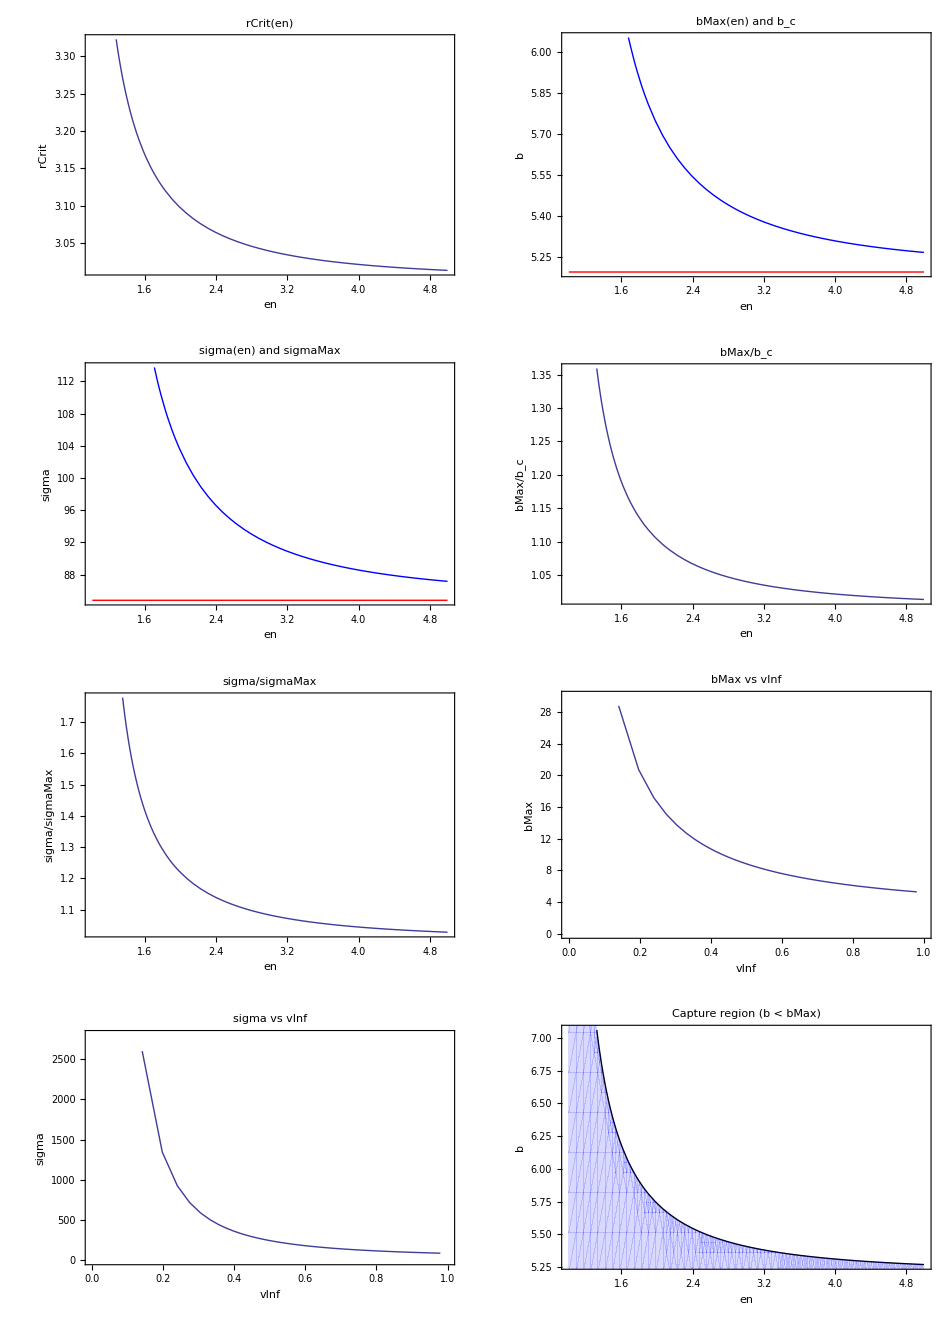

```mathematica
enMin = 1.01;
enMax = 5;

vInf[e_] := Sqrt[1 - 1/e^2];
img = 330;

p1 = Plot[rCrit[e], {e, enMin, enMax},
  Frame -> True,
  FrameLabel -> {"en", "rCrit"},
  PlotLabel -> "rCrit(en)",
  ImageSize -> img
  ];

p2 = Plot[{bMax[e], bPhoton}, {e, enMin, enMax},
  Frame -> True,
  FrameLabel -> {"en", "b"},
  PlotLabel -> "bMax(en) and b_c",
  PlotStyle -> {Blue, Red},
  ImageSize -> img
  ];

p3 = Plot[{sigma[e], sigmaMax}, {e, enMin, enMax},
  Frame -> True,
  FrameLabel -> {"en", "sigma"},
  PlotLabel -> "sigma(en) and sigmaMax",
  PlotStyle -> {Blue, Red},
  ImageSize -> img
  ];

p4 = Plot[bMax[e]/bPhoton, {e, enMin, enMax},
  Frame -> True,
  FrameLabel -> {"en", "bMax/b_c"},
  PlotLabel -> "bMax/b_c",
  ImageSize -> img
  ];

p5 = Plot[sigma[e]/sigmaMax, {e, enMin, enMax},
  Frame -> True,
  FrameLabel -> {"en", "sigma/sigmaMax"},
  PlotLabel -> "sigma/sigmaMax",
  ImageSize -> img
  ];

enList = Subdivide[enMin, enMax, 400];
ptsB = Table[{vInf[e], bMax[e]}, {e, enList}];
ptsS = Table[{vInf[e], sigma[e]}, {e, enList}];

p6 = ListLinePlot[ptsB,
  Frame -> True,
  FrameLabel -> {"vInf", "bMax"},
  PlotLabel -> "bMax vs vInf",
  PlotRange -> {{0, 1}, {0, 30}},
  ImageSize -> img
  ];

p7 = ListLinePlot[ptsS,
  Frame -> True,
  FrameLabel -> {"vInf", "sigma"},
  PlotLabel -> "sigma vs vInf",
  PlotRange -> {{0, 1}, {0, 2800}},
  ImageSize -> img
  ];

p8 = Show[
  Plot[bMax[e], {e, enMin, enMax},
   Frame -> True,
   FrameLabel -> {"en", "b"},
   PlotLabel -> "Capture region (b < bMax)",
   PlotStyle -> Black,
   ImageSize -> img
   ],
  RegionPlot[bb < bMax[ee], {ee, enMin, enMax}, {bb, 0, 15},
   PlotPoints -> 50,
   Mesh -> None,
   PlotStyle -> Directive[Opacity[0.15], Blue],
   BoundaryStyle -> None
   ]
  ];

GraphicsGrid[
 Partition[{p1, p2, p3, p4, p5, p6, p7, p8}, 2],
 Spacings -> {2, 2},
 ImageSize -> 950
 ]
```

## 9) Near-threshold scattering

Set b = b_max + delta b and scan capture vs escape close to the threshold.

b=b_max+δb

```mathematica
Manipulate[
 Module[
  {b0, bVal, data, xFar, rFun, phiFun, tauEnd, L, status, col, bh, orbitPlot},

  b0 = bMax[en];
  bVal = b0 + db;

  If[bVal <= 0,
   Framed[Style["need b = bMax + db > 0", 14, Red], FrameMargins -> 20],

   data = trajSolve[en, bVal];

   If[!AssociationQ[data],
    Framed[Style["No plot: run the setup cell first", 14, Red], FrameMargins -> 20],

   If[!TrueQ[data["ok"]],
    Framed[Style["No plot: " <> ToString[data["msg"]], 14, Red], FrameMargins -> 20],

    xFar = data["xFar"];
    rFun = data["r"];
    phiFun = data["phi"];
    tauEnd = data["tauEnd"];
    L = data["L"];

    status = If[TrueQ[data["captured"]], "CAPTURED", "ESCAPED"];
    col = If[TrueQ[data["captured"]], Red, Blue];

    bh = Graphics[{Black, Disk[{0, 0}, 2 M], Gray, Dashed, Circle[{0, 0}, 3 M]}];

    orbitPlot = Show[
      ParametricPlot[
       Evaluate[{rFun[t] Cos[phiFun[t]], rFun[t] Sin[phiFun[t]]}],
       {t, 0, tauEnd},
       PlotStyle -> col,
       PlotRange -> {{-xFar, xFar}, {-xFar, xFar}},
       Frame -> True, AspectRatio -> 1,
       FrameLabel -> {"x", "y"},
       PlotLabel -> Style[status, 16, Bold, col]
       ],
      bh
      ];

    Column[{
      Style["Near-threshold scan (b = bMax + db)", Bold, 14],
      Row[{"en = ", NumberForm[en, {5, 3}], "    bMax = ", NumberForm[b0, {6, 4}], "    b = ", NumberForm[bVal, {6, 4}]}],
      orbitPlot
      }]
    ]
    ]
   ]
  ],
 {{en, 1.35, "en"}, 1.01, 3, 0.001, Appearance -> "Labeled"},
 {{db, 0, "db = b - bMax"}, -3, 3, 0.001, Appearance -> "Labeled"},
 ControlPlacement -> Left,
 TrackedSymbols :> {en, db}
 ]
```

## 10) Three trajectories near b_max

Compare b<b_max, b=b_max, b>b_max at the same energy.

```mathematica
Manipulate[
 Module[
  {b0, bs, sols, cols, labels, xFar, bh, plots, legendG},

  b0 = bMax[en];
  bs = {b0 - d, b0, b0 + d};

  cols = {Red, Black, Blue};
  labels = {"b<bMax", "b=bMax", "b>bMax"};

  sols = trajSolve[en, #, 30., 2500.] & /@ bs;

  If[!AssociationQ[sols[[1]]],
   Framed[Style["No plot: run the setup cell first", 14, Red], FrameMargins -> 20],

  xFar = 30.;
  bh = Graphics[{Black, Disk[{0, 0}, 2 M], Gray, Dashed, Circle[{0, 0}, 3 M]}];

  plots = Table[
    If[TrueQ[sols[[i]]["ok"]],
     With[{rFun = sols[[i]]["r"], phiFun = sols[[i]]["phi"], tauEnd = sols[[i]]["tauEnd"]},
      ParametricPlot[
       Evaluate[{rFun[t] Cos[phiFun[t]], rFun[t] Sin[phiFun[t]]}],
       {t, 0, tauEnd},
       PlotStyle -> cols[[i]]
       ]
      ],
     Graphics[{}]
     ],
    {i, 1, 3}
    ];

  legendG = Graphics[{
      Text[Style[labels[[1]], 12, cols[[1]]], Scaled[{0.82, 0.92}]],
      Text[Style[labels[[2]], 12, cols[[2]]], Scaled[{0.82, 0.87}]],
      Text[Style[labels[[3]], 12, cols[[3]]], Scaled[{0.82, 0.82}]]
      }];

  Show[
   bh,
   Evaluate[Sequence @@ plots],
   legendG,
   PlotRange -> {{-xFar, xFar}, {-xFar, xFar}},
   Frame -> True, AspectRatio -> 1,
   FrameLabel -> {"x", "y"},
   PlotLabel -> Style[Row[{"3 trajectories near bMax   (en = ", NumberForm[en, {5, 3}], ")"}], 14, Bold]
   ]
   ]
  ],
 {{en, 2.77, "en"}, 1.01, 5, 0.01, Appearance -> "Labeled"},
 {{d, 0.2, "offset d"}, 0, 3, 0.01, Appearance -> "Labeled"},
 ControlPlacement -> Left,
 TrackedSymbols :> {en, d}
 ]
```